```mathematica
SetDirectory["/Users/padamson/research/seamless/spec/fig"]
```

/Users/padamson/research/seamless/spec/fig

```mathematica
plotWithRightRectangles[a_,b_,n_,f_,xRange_,yRange_]:=
Module[{},
rightRectangleList=rightRectangles[a,b,n,f];
areaList=
Table[
(rightRectangleList[[i,3,2,1]]-rightRectangleList[[i,3,1,1]])*rightRectangleList[[i,3,2,2]],
{i,1,n}
];
function=Inset[f[x],
{xRange[[1]]+0.5*(xRange[[2]]-xRange[[1]]),
yRange[[1]]+0.9*(yRange[[2]]-yRange[[1]])}
];
exactIntegral=
Text[
StringJoin[
"Exact integral: ",
ToString[Evaluate[Integrate[f[x],{x,a,b}]]]
],
{xRange[[1]]+0.5*(xRange[[2]]-xRange[[1]]),
yRange[[1]]+0.7*(yRange[[2]]-yRange[[1]])}
];
areaListGraphic=Table[
Inset[
NumberForm[
areaList[[i]],
2
],
centerOfRectangle[rightRectangleList[[i,3]]]
],
{i,1,n}
];
areaSum=
Text[
StringJoin[
"Total Area of Rectangles: ",
ToString[
NumberForm[
Sum[
areaList[[i]],{i,1,n}
],
5
]
]
],
{xRange[[1]]+0.5*(xRange[[2]]-xRange[[1]]),
yRange[[1]]+0.8*(yRange[[2]]-yRange[[1]])}
];
Plot[f[x],{x,xRange[[1]],xRange[[2]]},
PlotRange->yRange,
Frame->True,
Prolog->{rightRectangleList,areaListGraphic,areaSum},
ImageSize->400,
FrameLabel->{"x","f(x)"}
]
]
```

```mathematica
rightRectangles[a_,b_,n_,f_]:=
Module[{},
xBottomLeftList=Table[a+i (b-a)/n,{i,0,n}];
Table[
{EdgeForm[Dashed],LightBlue,
Rectangle[
{xBottomLeftList[[i]],0},
{xBottomLeftList[[i+1]],f[xBottomLeftList[[i+1]]]}
]},
{i,1,n}
]
]
```

```mathematica
centerOfRectangle[rectangle_]:=
{rectangle[[1,1]]+.5*(rectangle[[2,1]]-rectangle[[1,1]]),
rectangle[[1,2]]+.5*(rectangle[[2,2]]-rectangle[[1,2]])}
```

```mathematica
f[x_]:=(2 x-.5)^3+(1.5 x-1)^2-x+1;
```

```mathematica
Do[
filename = StringJoin[Directory[],"/rightrectangle-",ToString[n],".eps"];
Export[filename, plotWithRightRectangles[.1,.8,n,f,{0,1},{0,4}]],
{n,{4,6,10}}
]
```

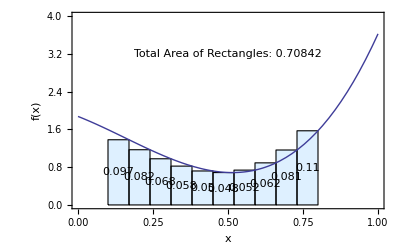

```mathematica
plotWithRightRectangles[.1,.8,10,f,{0,1},{0,4}]
```

```mathematica
Integrate[f[x],{x,.1,.8}]
```

0.70525

```mathematica
TeXForm[f[x]]
```

(2 x-0.5)^3+(1.5 x-1)^2-x+1

```mathematica
Simplify[(a+n h+a+(n+1) h)/2]
```

0.005+1. a+0.01 n

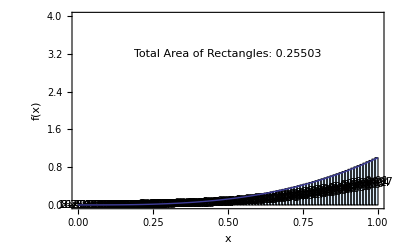

```mathematica
f[x_]:=x^3;
plotWithRightRectangles[0.,1.,100,f,{0,1},{0,4}]
```

```mathematica
leftRectangleMaximumError[a_,b_,N_,f_]:=Module[{},
(b-a)/N*(f[b]-f[a])
];
```

```mathematica
leftRectangleMaximumError[0.0,1.0,100,f]
```

0.01